## Work Code Samples

```mathematica
DirectedGraph@AdjacencyGraph[ConstantArray[1,{4,4}],GraphLayout->"RadialEmbedding"]
```

-Graphics-

```mathematica
CommunityGraphPlot[Graph[DirectedEdge@@@RandomInteger[100,{200,2}]]]
```

-Graphics-

```mathematica
Alphabet[]
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z}

```mathematica
Style[Alphabet[],20]
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z}

```mathematica
Style[#,20]&/@Alphabet[]
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z}

```mathematica
Rasterize[Style[#,20]]&/@Alphabet[]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
NearestNeighborGraph[Rasterize[Style[#,20]]&/@Alphabet[],2,VertexLabels->Automatic]
```

-Graphics-

```mathematica
TextRecognize[Blur[Rasterize[Style["hello",50]],#]]&/@Range[10]
```

{hello,hello,hello,hello,hello,hello,hello,hello,hello,hello}

```mathematica
Dendrogram[Rasterize/@Alphabet[]]
```

-Graphics-

```mathematica
Dendrogram[Rasterize/@Take[Alphabet[],10]]
```

-Graphics-

```mathematica
FeatureSpacePlot[Rasterize[ToUpperCase[#]]&/@Alphabet[]]
```

-Graphics-

```mathematica
ImageIdentify[Blur[Entity["Building","EiffelTower::5h9w8"]["Image"],#]]&/@Range[5]
```

{Eiffel Tower,Eiffel Tower,tower,stupa,stupa}

```mathematica
Classify["Sentiment",WikipediaData["happiness"]]
```

Neutral

```mathematica
Nearest[Table[Hue[h],{h,0,1,0.05}],Pink,3]
```

{Hue[0.9500000000000001],Hue[0.9],Hue[0.05]}

```mathematica
Table[i/j,{i,500},{j,500}]
```

```mathematica
First[Table[i/j,{i,500},{j,500}]]
```

{1,1/2,1/3,1/4,1/5,1/6,1/7,1/8,1/9,1/10,1/11,1/12,1/13,1/14,1/15,1/16,1/17,1/18,1/19,1/20,1/21,1/22,1/23,1/24,1/25,1/26,1/27,1/28,1/29,1/30,1/31,1/32,1/33,1/34,1/35,1/36,1/37,1/38,1/39,1/40,1/41,1/42,1/43,1/44,1/45,1/46,1/47,1/48,1/49,1/50,1/51,1/52,1/53,1/54,1/55,1/56,1/57,1/58,1/59,1/60,1/61,1/62,1/63,1/64,1/65,1/66,1/67,1/68,1/69,1/70,1/71,1/72,1/73,1/74,1/75,1/76,1/77,1/78,1/79,1/80,1/81,1/82,1/83,1/84,1/85,1/86,1/87,1/88,1/89,1/90,1/91,1/92,1/93,1/94,1/95,1/96,1/97,1/98,1/99,1/100,1/101,1/102,1/103,1/104,1/105,1/106,1/107,1/108,1/109,1/110,1/111,1/112,1/113,1/114,1/115,1/116,1/117,1/118,1/119,1/120,1/121,1/122,1/123,1/124,1/125,1/126,1/127,1/128,1/129,1/130,1/131,1/132,1/133,1/134,1/135,1/136,1/137,1/138,1/139,1/140,1/141,1/142,1/143,1/144,1/145,1/146,1/147,1/148,1/149,1/150,1/151,1/152,1/153,1/154,1/155,1/156,1/157,1/158,1/159,1/160,1/161,1/162,1/163,1/164,1/165,1/166,1/167,1/168,1/169,1/170,1/171,1/172,1/173,1/174,1/175,1/176,1/177,1/178,1/179,1/180,1/181,1/182,1/183,1/184,1/185,1/186,1/187,1/188,1/189,1/190,1/191,1/192,1/193,1/194,1/195,1/196,1/197,1/198,1/199,1/200,1/201,1/202,1/203,1/204,1/205,1/206,1/207,1/208,1/209,1/210,1/211,1/212,1/213,1/214,1/215,1/216,1/217,1/218,1/219,1/220,1/221,1/222,1/223,1/224,1/225,1/226,1/227,1/228,1/229,1/230,1/231,1/232,1/233,1/234,1/235,1/236,1/237,1/238,1/239,1/240,1/241,1/242,1/243,1/244,1/245,1/246,1/247,1/248,1/249,1/250,1/251,1/252,1/253,1/254,1/255,1/256,1/257,1/258,1/259,1/260,1/261,1/262,1/263,1/264,1/265,1/266,1/267,1/268,1/269,1/270,1/271,1/272,1/273,1/274,1/275,1/276,1/277,1/278,1/279,1/280,1/281,1/282,1/283,1/284,1/285,1/286,1/287,1/288,1/289,1/290,1/291,1/292,1/293,1/294,1/295,1/296,1/297,1/298,1/299,1/300,1/301,1/302,1/303,1/304,1/305,1/306,1/307,1/308,1/309,1/310,1/311,1/312,1/313,1/314,1/315,1/316,1/317,1/318,1/319,1/320,1/321,1/322,1/323,1/324,1/325,1/326,1/327,1/328,1/329,1/330,1/331,1/332,1/333,1/334,1/335,1/336,1/337,1/338,1/339,1/340,1/341,1/342,1/343,1/344,1/345,1/346,1/347,1/348,1/349,1/350,1/351,1/352,1/353,1/354,1/355,1/356,1/357,1/358,1/359,1/360,1/361,1/362,1/363,1/364,1/365,1/366,1/367,1/368,1/369,1/370,1/371,1/372,1/373,1/374,1/375,1/376,1/377,1/378,1/379,1/380,1/381,1/382,1/383,1/384,1/385,1/386,1/387,1/388,1/389,1/390,1/391,1/392,1/393,1/394,1/395,1/396,1/397,1/398,1/399,1/400,1/401,1/402,1/403,1/404,1/405,1/406,1/407,1/408,1/409,1/410,1/411,1/412,1/413,1/414,1/415,1/416,1/417,1/418,1/419,1/420,1/421,1/422,1/423,1/424,1/425,1/426,1/427,1/428,1/429,1/430,1/431,1/432,1/433,1/434,1/435,1/436,1/437,1/438,1/439,1/440,1/441,1/442,1/443,1/444,1/445,1/446,1/447,1/448,1/449,1/450,1/451,1/452,1/453,1/454,1/455,1/456,1/457,1/458,1/459,1/460,1/461,1/462,1/463,1/464,1/465,1/466,1/467,1/468,1/469,1/470,1/471,1/472,1/473,1/474,1/475,1/476,1/477,1/478,1/479,1/480,1/481,1/482,1/483,1/484,1/485,1/486,1/487,1/488,1/489,1/490,1/491,1/492,1/493,1/494,1/495,1/496,1/497,1/498,1/499,1/500}

```mathematica
Last[Table[i/j,{i,500},{j,500}]]
```

{500,250,500/3,125,100,250/3,500/7,125/2,500/9,50,500/11,125/3,500/13,250/7,100/3,125/4,500/17,250/9,500/19,25,500/21,250/11,500/23,125/6,20,250/13,500/27,125/7,500/29,50/3,500/31,125/8,500/33,250/17,100/7,125/9,500/37,250/19,500/39,25/2,500/41,250/21,500/43,125/11,100/9,250/23,500/47,125/12,500/49,10,500/51,125/13,500/53,250/27,100/11,125/14,500/57,250/29,500/59,25/3,500/61,250/31,500/63,125/16,100/13,250/33,500/67,125/17,500/69,50/7,500/71,125/18,500/73,250/37,20/3,125/19,500/77,250/39,500/79,25/4,500/81,250/41,500/83,125/21,100/17,250/43,500/87,125/22,500/89,50/9,500/91,125/23,500/93,250/47,100/19,125/24,500/97,250/49,500/99,5,500/101,250/51,500/103,125/26,100/21,250/53,500/107,125/27,500/109,50/11,500/111,125/28,500/113,250/57,100/23,125/29,500/117,250/59,500/119,25/6,500/121,250/61,500/123,125/31,4,250/63,500/127,125/32,500/129,50/13,500/131,125/33,500/133,250/67,100/27,125/34,500/137,250/69,500/139,25/7,500/141,250/71,500/143,125/36,100/29,250/73,500/147,125/37,500/149,10/3,500/151,125/38,500/153,250/77,100/31,125/39,500/157,250/79,500/159,25/8,500/161,250/81,500/163,125/41,100/33,250/83,500/167,125/42,500/169,50/17,500/171,125/43,500/173,250/87,20/7,125/44,500/177,250/89,500/179,25/9,500/181,250/91,500/183,125/46,100/37,250/93,500/187,125/47,500/189,50/19,500/191,125/48,500/193,250/97,100/39,125/49,500/197,250/99,500/199,5/2,500/201,250/101,500/203,125/51,100/41,250/103,500/207,125/52,500/209,50/21,500/211,125/53,500/213,250/107,100/43,125/54,500/217,250/109,500/219,25/11,500/221,250/111,500/223,125/56,20/9,250/113,500/227,125/57,500/229,50/23,500/231,125/58,500/233,250/117,100/47,125/59,500/237,250/119,500/239,25/12,500/241,250/121,500/243,125/61,100/49,250/123,500/247,125/62,500/249,2,500/251,125/63,500/253,250/127,100/51,125/64,500/257,250/129,500/259,25/13,500/261,250/131,500/263,125/66,100/53,250/133,500/267,125/67,500/269,50/27,500/271,125/68,500/273,250/137,20/11,125/69,500/277,250/139,500/279,25/14,500/281,250/141,500/283,125/71,100/57,250/143,500/287,125/72,500/289,50/29,500/291,125/73,500/293,250/147,100/59,125/74,500/297,250/149,500/299,5/3,500/301,250/151,500/303,125/76,100/61,250/153,500/307,125/77,500/309,50/31,500/311,125/78,500/313,250/157,100/63,125/79,500/317,250/159,500/319,25/16,500/321,250/161,500/323,125/81,20/13,250/163,500/327,125/82,500/329,50/33,500/331,125/83,500/333,250/167,100/67,125/84,500/337,250/169,500/339,25/17,500/341,250/171,500/343,125/86,100/69,250/173,500/347,125/87,500/349,10/7,500/351,125/88,500/353,250/177,100/71,125/89,500/357,250/179,500/359,25/18,500/361,250/181,500/363,125/91,100/73,250/183,500/367,125/92,500/369,50/37,500/371,125/93,500/373,250/187,4/3,125/94,500/377,250/189,500/379,25/19,500/381,250/191,500/383,125/96,100/77,250/193,500/387,125/97,500/389,50/39,500/391,125/98,500/393,250/197,100/79,125/99,500/397,250/199,500/399,5/4,500/401,250/201,500/403,125/101,100/81,250/203,500/407,125/102,500/409,50/41,500/411,125/103,500/413,250/207,100/83,125/104,500/417,250/209,500/419,25/21,500/421,250/211,500/423,125/106,20/17,250/213,500/427,125/107,500/429,50/43,500/431,125/108,500/433,250/217,100/87,125/109,500/437,250/219,500/439,25/22,500/441,250/221,500/443,125/111,100/89,250/223,500/447,125/112,500/449,10/9,500/451,125/113,500/453,250/227,100/91,125/114,500/457,250/229,500/459,25/23,500/461,250/231,500/463,125/116,100/93,250/233,500/467,125/117,500/469,50/47,500/471,125/118,500/473,250/237,20/19,125/119,500/477,250/239,500/479,25/24,500/481,250/241,500/483,125/121,100/97,250/243,500/487,125/122,500/489,50/49,500/491,125/123,500/493,250/247,100/99,125/124,500/497,250/249,500/499,1}

```mathematica
Nearest[Flatten[Table[i/j,{i,500},{j,500}]],Pi,10]
```

{355/113,377/120,333/106,399/127,311/99,421/134,443/141,289/92,465/148,487/155}

```mathematica
RandomInteger[10,10]
```

{2,6,3,10,8,4,10,1,7,0}

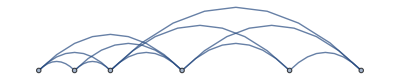

```mathematica
NearestNeighborGraph[RandomInteger[10,10],3]
```

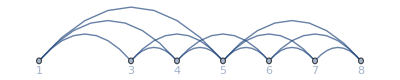

```mathematica
NearestNeighborGraph[RandomInteger[10,10],3,VertexLabels->Automatic]
```

```mathematica
RandomColor[100]
```

{RGBColor[0.5105228221473481, 0.9395786685995142, 0.884714714831184],RGBColor[0.4558251975700136, 0.0541491970875132, 0.48123473496830105],RGBColor[0.7042053170704001, 0.6208223250795679, 0.43209658611856816],RGBColor[0.6189335169996637, 0.6951428299321838, 0.8400266530411897],RGBColor[0.2779503974636852, 0.5236295706956982, 0.8881628240046406],RGBColor[0.12723042373492488, 0.938290969705077, 0.7605082141248527],RGBColor[0.6108233946170263, 0.9276211781543577, 0.01347415511067429],RGBColor[0.20719025858720252, 0.1949810157633165, 0.2275785558591754],RGBColor[0.38733071738251135, 0.6752190656973489, 0.9099552108360076],RGBColor[0.6953250974563017, 0.5656522515997815, 0.015207869095106075],RGBColor[0.8934093010707378, 0.7019985493567731, 0.9206672050115521],RGBColor[0.991471206532079, 0.55223113842785, 0.33976049849566525],RGBColor[0.44385438647685893, 0.6685115625362945, 0.7534813049286928],RGBColor[0.5847522742261186, 0.5875976332208632, 0.03202143251478318],RGBColor[0.6178763930690045, 0.8114599783726646, 0.7645549506337241],RGBColor[0.2457949838099689, 0.20399815298329105, 0.22580215972550688],RGBColor[0.11617583522129005, 0.9938597623656715, 0.3436334981154012],RGBColor[0.690090257806973, 0.9455230391431764, 0.4740065775367577],RGBColor[0.6061480627437572, 0.09524581376093888, 0.23192938448601907],RGBColor[0.3686159240230322, 0.44938323778905875, 0.6987204631299064],RGBColor[0.09533840571716978, 0.469394633707896, 0.17691452468329616],RGBColor[0.12151513060645192, 0.5173698248498395, 0.6058009158498014],RGBColor[0.7538492117346158, 0.866671382588172, 0.17635503444993028],RGBColor[0.7222829149612802, 0.7266497805023302, 0.4307756661217652],RGBColor[0.5218939802756579, 0.608272644737812, 0.6633324586413578],RGBColor[0.4945300236365746, 0.2758789023528754, 0.07887048774677852],RGBColor[0.08982016253550773, 0.9452941352672923, 0.1782918604931072],RGBColor[0.7460439898699822, 0.31936893300559044, 0.3643933262543322],RGBColor[0.39506669684076967, 0.40035215156629667, 0.14769440843730464],RGBColor[0.7709077022231681, 0.6075462021089009, 0.1655606024886076],RGBColor[0.9538199103580203, 0.7402383468448748, 0.49562781919666965],RGBColor[0.5352745844436826, 0.5269122750713964, 0.7864964759640125],RGBColor[0.9642139749082665, 0.37942478066043095, 0.6289204457458342],RGBColor[0.35080142061364783, 0.6432525490494638, 0.255336581435365],RGBColor[0.008486523923169065, 0.6742925816726166, 0.4124465772092085],RGBColor[0.6958029335061504, 0.011730824355907998, 0.597315667071199],RGBColor[0.5978687231781459, 0.7403471742985548, 0.7532277806491672],RGBColor[0.6897955574556567, 0.8401044406675031, 0.5361288947654803],RGBColor[0.08612034313572137, 0.36162519818433947, 0.365368363635191],RGBColor[0.6043899159337209, 0.28846174662905577, 0.34044341664705335],RGBColor[0.41037220381110884, 0.9103810352618573, 0.8460683432226994],RGBColor[0.33141641314323134, 0.8269332576374193, 0.595119851871283],RGBColor[0.6437320437493312, 0.5607851863792923, 0.7206290400073061],RGBColor[0.689205448156279, 0.09923796639135007, 0.2067058941543236],RGBColor[0.5463638972148179, 0.27447762575855883, 0.6864930423465956],RGBColor[0.5572400230769283, 0.04094370940127012, 0.7110228752759511],RGBColor[0.8798160356451417, 0.23115319054307037, 0.25558411839911743],RGBColor[0.04917511838432698, 0.08729588260180288, 0.3952673311325172],RGBColor[0.7679803109810279, 0.5907913566541954, 0.9211016342748142],RGBColor[0.7040703642711197, 0.9951130467967664, 0.10020444638466564],RGBColor[0.7723057557442294, 0.6987133683374736, 0.28590676271890003],RGBColor[0.3936736381956849, 0.5337690706024887, 0.018848327480759597],RGBColor[0.17808277042817888, 0.7986820195493443, 0.3630557888423718],RGBColor[0.7096847439672309, 0.13703099333220337, 0.46407403808894365],RGBColor[0.5481080591396155, 0.7566667100030475, 0.2696496937380253],RGBColor[0.7884825209640625, 0.11194060775839265, 0.3196855212172056],RGBColor[0.7807200188554022, 0.5163472713178938, 0.23266496601026998],RGBColor[0.11728886429502428, 0.7490375086222931, 0.3063374909954213],RGBColor[0.08905677872114226, 0.21470063395484074, 0.4710461350966282],RGBColor[0.7059611623635642, 0.2457314365457286, 0.29819544283645993],RGBColor[0.9084164518658961, 0.19000537038437137, 0.26393462051527194],RGBColor[0.8211604819489959, 0.8798514140688907, 0.7210780178196887],RGBColor[0.9426486325491383, 0.7391103964689472, 0.04103061132816599],RGBColor[0.8196849957646435, 0.5849518053366394, 0.8596310054930618],RGBColor[0.1322059694446791, 0.656954222644685, 0.10854912777016201],RGBColor[0.6980943731528122, 0.9751247453750616, 0.55330306567466],RGBColor[0.6371742412337622, 0.12824887646046212, 0.9846049662612868],RGBColor[0.4722051306804813, 0.859631813497381, 0.334665952772615],RGBColor[0.6602224330116937, 0.6217287740003354, 0.8654941762876871],RGBColor[0.9675981051774765, 0.9632454560527461, 0.4941504824430436],RGBColor[0.9678633368489307, 0.29363068514656, 0.5036885460743952],RGBColor[0.2886839158802026, 0.31511048198883684, 0.9824423951676822],RGBColor[0.20303328554821753, 0.9551996910164076, 0.2597789407616167],RGBColor[0.7028601291532943, 0.8867260142284563, 0.3603482082638254],RGBColor[0.23148911644365278, 0.6894305549883444, 0.2699229868235691],RGBColor[0.8518353151867981, 0.8129821971299458, 0.07838130104260199],RGBColor[0.8099082661750518, 0.03765003551404211, 0.08994409334849296],RGBColor[0.6683869709656465, 0.7348235713371336, 0.7625990420471396],RGBColor[0.5113469714385537, 0.7164940366324173, 0.005099113229557917],RGBColor[0.6464360360372781, 0.6572575518201416, 0.9230472976801682],RGBColor[0.24492434566783294, 0.8046742738727253, 0.396189314616197],RGBColor[0.07470283157402258, 0.7203025091633763, 0.9542976108197678],RGBColor[0.9028692164193768, 0.7869877046403546, 0.9036714279958564],RGBColor[0.003049329316381355, 0.062307858601856836, 0.08169576080149366],RGBColor[0.795470205935487, 0.3775484379985117, 0.8072399956981378],RGBColor[0.05427460541780982, 0.21848235326972731, 0.9978199517953568],RGBColor[0.8492442473715249, 0.8090680139611715, 0.8709312756028187],RGBColor[0.6827546503507309, 0.7016206154191422, 0.42861161432156436],RGBColor[0.9554196745234071, 0.19305274485074464, 0.5162829437684955],RGBColor[0.023846896481386493, 0.48618050450042727, 0.20089439929382857],RGBColor[0.5588591851182563, 0.326172834063714, 0.9193670813008308],RGBColor[0.8407387789443785, 0.14108789564425028, 0.9226275109735056],RGBColor[0.3517548294082089, 0.297590475595497, 0.2598439494020224],RGBColor[0.642676708225796, 0.9300592528118428, 0.15094027562472578],RGBColor[0.21950542352721403, 0.6739280930131066, 0.1379447042043298],RGBColor[0.7526803978776235, 0.9941963963379901, 0.19775180039123263],RGBColor[0.7525908264571153, 0.8681382423256718, 0.375554990873747],RGBColor[0.8579813410820891, 0.5384464706883085, 0.3883720201952623],RGBColor[0.9826739263163213, 0.7015230445029514, 0.34556612167590295],RGBColor[0.4822517757821294, 0.1700463542007653, 0.5687288147964009]}

```mathematica
FindClusters[RandomColor[100]]
```

{{RGBColor[0.1895725848174088, 0.4125524278815471, 0.21027103175866335],RGBColor[0.6160636883709314, 0.7376795954957682, 0.2743236621976277],RGBColor[0.3072866040867561, 0.4085638919245118, 0.042762228068248476],RGBColor[0.02336398412635332, 0.8056346377396397, 0.06571182463993952],RGBColor[0.05408310769886704, 0.9367582475768808, 0.09270325157260473],RGBColor[0.7794038777860284, 0.969029260210575, 0.10245389664970395],RGBColor[0.5607134661846433, 0.9361491753829017, 0.2929997274689764],RGBColor[0.09806967572418879, 0.5690043225300112, 0.22697899233501428],RGBColor[0.7603274899333103, 0.8235954343844538, 0.2039970984564674],RGBColor[0.4725027521168814, 0.6513113434229991, 0.07750335983760204],RGBColor[0.3527320367164226, 0.8258392341820708, 0.00323276014246332],RGBColor[0.31299787033106075, 0.5748658606804322, 0.18020945094594176],RGBColor[0.7033014657131256, 0.8419188544915046, 0.49862116985260285],RGBColor[0.669242039801957, 0.8816544877208734, 0.5632520346280132],RGBColor[0.569610208337777, 0.8481112302596843, 0.32098976642742105],RGBColor[0.44091492526818965, 0.42173866187910347, 0.055532151333284485],RGBColor[0.2203638427671204, 0.9190109511888953, 0.19569029420642825]},{RGBColor[0.5863700624326134, 0.15782113079391014, 0.8665045463260581],RGBColor[0.6670512797326251, 0.2406940815040426, 0.6084727441600049],RGBColor[0.24714028212677408, 0.3692837065749073, 0.8219233862379487],RGBColor[0.10688934562796737, 0.6192193943305331, 0.6147406656867762],RGBColor[0.3446074495415681, 0.4614339449456919, 0.8458879077335626],RGBColor[0.4713187848055169, 0.06165682757126567, 0.21980846256730313],RGBColor[0.3524585219222083, 0.7329243572517541, 0.8199627262339946],RGBColor[0.8254982913214617, 0.5865655597200856, 0.6501439229643651],RGBColor[0.0763165671512962, 0.33561714211339044, 0.42723406784740314],RGBColor[0.718538762253915, 0.22898236270749894, 0.818010696117164],RGBColor[0.5643500278729998, 0.17507814631144902, 0.8192170114775301],RGBColor[0.11894092767263609, 0.46091150565736627, 0.8114513609939857],RGBColor[0.1312315591339892, 0.33975420695201985, 0.9371946504698405],RGBColor[0.2158658201390946, 0.31309862129717314, 0.9490314243316178],RGBColor[0.7360343065897887, 0.12596436635148134, 0.194918759976197],RGBColor[0.21494517045029915, 0.12863047381536696, 0.5984184007805529],RGBColor[0.8086963097344133, 0.21264776351922965, 0.3979016010469347],RGBColor[0.6589485416809542, 0.3404264306713982, 0.2759954592846692],RGBColor[0.31347523848582814, 0.4173475557346642, 0.8891469301233248],RGBColor[0.4045275944770199, 0.24478665672394473, 0.955710864130042],RGBColor[0.9339852784664326, 0.6791175715322793, 0.596576627207283],RGBColor[0.8778681260367907, 0.03610999816556948, 0.44490411450852374],RGBColor[0.6718425461659678, 0.4982375968217838, 0.7290125190751937],RGBColor[0.02894294142751308, 0.3562490776177567, 0.7568361933349461],RGBColor[0.07970099760485372, 0.04775602233425413, 0.0370911560505629],RGBColor[0.4110777159780188, 0.21877493828473948, 0.7260111824003366],RGBColor[0.8369120047494625, 0.7379923634671088, 0.6922832232363756],RGBColor[0.9496409769210281, 0.2656283523255185, 0.36827584608042097],RGBColor[0.1555144904124841, 0.7429007094788393, 0.9918592997424833],RGBColor[0.29544082797615334, 0.36575282329973313, 0.6849193578595179],RGBColor[0.6243868711049114, 0.0721389292569421, 0.4552479616698879],RGBColor[0.6730676693003992, 0.28476733520906694, 0.4169697999952118],RGBColor[0.23357335961029313, 0.6227166084157312, 0.501804069204496],RGBColor[0.818578290404337, 0.4202258108801833, 0.4624973196478195],RGBColor[0.30289557190523486, 0.25821861530104306, 0.18284194033381018],RGBColor[0.2044003991585681, 0.3706844709648103, 0.6152096816118215],RGBColor[0.34394637964882535, 0.14438876491976327, 0.5567072519365148],RGBColor[0.490704352801254, 0.3061946843058072, 0.22146257230080924],RGBColor[0.9200561458548746, 0.9445483974253341, 0.937565157646054],RGBColor[0.15348674040981325, 0.3019211526578156, 0.8751734833483726],RGBColor[0.9544503623577751, 0.5659601353217583, 0.4271676718373698],RGBColor[0.983043172095919, 0.19334115952402686, 0.9890561319699238],RGBColor[0.4693183360625237, 0.6636224930177799, 0.8209294787713548],RGBColor[0.31732258295340743, 0.011848141880425489, 0.41333285406723785],RGBColor[0.5952599000086687, 0.45226228015756065, 0.8131132943506918],RGBColor[0.4984472048492796, 0.4998088224757813, 0.39574444808614717],RGBColor[0.8116140732009822, 0.6481555176024556, 0.8785544144325625],RGBColor[0.9685814420375123, 0.2631724533937343, 0.575854016067116],RGBColor[0.5043732320758822, 0.016799944319662474, 0.25801442801842156],RGBColor[0.9128543040594967, 0.33361074943185454, 0.8440726974834418],RGBColor[0.1467773823499241, 0.22463578720774735, 0.2500552683958581],RGBColor[0.08646412310852836, 0.6370162608788497, 0.5896241235945829],RGBColor[0.20287552745848103, 0.12374639502463358, 0.6721918969273224],RGBColor[0.41122709035464466, 0.5352673773614685, 0.8657440676079287],RGBColor[0.6284517340704645, 0.613251017557854, 0.6824831898088977],RGBColor[0.34199101241004315, 0.7943461158778113, 0.978552021920603],RGBColor[0.7292757935569405, 0.4337198815636383, 0.6176385631949066],RGBColor[0.3299893881459217, 0.36720423448409933, 0.7800528513172476],RGBColor[0.8915563244689766, 0.41224923956647563, 0.24547725636412898],RGBColor[0.14805008815690823, 0.047840709407043214, 0.6418274081051747],RGBColor[0.7918892112008062, 0.454006508499341, 0.3736597113026059],RGBColor[0.09734977879104356, 0.15560079478909428, 0.8216629852151243],RGBColor[0.715495251962784, 0.0342391402266633, 0.5229249127461768],RGBColor[0.18361835450930064, 0.5856413887821912, 0.9053564872739697],RGBColor[0.6444405500488712, 0.18182897360702044, 0.36688335645490944],RGBColor[0.7542875970099439, 0.5544439338790448, 0.9562639239211086],RGBColor[0.540407618506664, 0.4018941810625978, 0.7394231715171973],RGBColor[0.5290841080438216, 0.25050087212676053, 0.4750648421307524],RGBColor[0.05509973038292504, 0.3423987242814741, 0.5558238287910635],RGBColor[0.9853649227457115, 0.008949861533977588, 0.7240429308750886],RGBColor[0.5261458383794579, 0.31797414620331077, 0.28988066649046274],RGBColor[0.8911682720800416, 0.47027209342750154, 0.4520160352030014],RGBColor[0.49917334018563375, 0.125290511111384, 0.8405202443048554],RGBColor[0.9180789302732935, 0.09018487305622869, 0.3199538560839206],RGBColor[0.47052326677815404, 0.21211859366360297, 0.8610016862170022]},{RGBColor[0.839872922818713, 0.7287143892644756, 0.4815926922598113],RGBColor[0.9625665130521721, 0.8434498213496187, 0.6416723491124541],RGBColor[0.8204064329737808, 0.7508823123409691, 0.4444619734299129],RGBColor[0.8597468644595145, 0.733270799844659, 0.4139913178954]},{RGBColor[0.9054735885456124, 0.5299780187843961, 0.13222184798858772],RGBColor[0.8286617939933514, 0.5162922911557526, 0.07348135235242181]},{RGBColor[0.12496356122441998, 0.8862199266795556, 0.6347417595132903],RGBColor[0.05933424295028855, 0.8781372001113732, 0.5480608311526558]}}

```mathematica
{#,ToUpperCase[#]}&/@Alphabet[]
```

{{a,A},{b,B},{c,C},{d,D},{e,E},{f,F},{g,G},{h,H},{i,I},{j,J},{k,K},{l,L},{m,M},{n,N},{o,O},{p,P},{q,Q},{r,R},{s,S},{t,T},{u,U},{v,V},{w,W},{x,X},{y,Y},{z,Z}}

```mathematica
Flatten[{#,ToUpperCase[#]}&/@Alphabet[]]
```

{a,A,b,B,c,C,d,D,e,E,f,F,g,G,h,H,i,I,j,J,k,K,l,L,m,M,n,N,o,O,p,P,q,Q,r,R,s,S,t,T,u,U,v,V,w,W,x,X,y,Y,z,Z}

```mathematica
Rasterize/@Flatten[{#,ToUpperCase[#]}&/@Alphabet[]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
FeatureSpacePlot[Rasterize/@Flatten[{#,ToUpperCase[#]}&/@Alphabet[]]]
```

-Graphics-

```mathematica
N[Pi,50]
```

3.1415926535897932384626433832795028841971693993751

```mathematica
N[Pi,50]-Round[Pi]
```

0.141592653589793238462643383279502884197169399375

```mathematica
Sum[Prime[i],{i,1000}]
```

3682913

```mathematica
Total[Prime[Range[1000]]]
```

3682913

```mathematica
Mod[Prime[Range[100]],4]
```

{2,3,1,3,3,1,1,3,3,1,3,1,1,3,3,1,3,1,3,3,1,3,3,1,1,1,3,3,1,1,3,3,1,3,1,3,1,3,3,1,3,1,3,1,1,3,3,3,3,1,1,3,1,3,1,3,1,3,1,1,3,1,3,3,1,1,3,1,3,1,1,3,3,1,3,3,1,1,1,1,3,1,3,1,3,3,1,1,1,3,3,3,3,3,3,3,1,1,3,1}

```mathematica
90° Mod[Prime[Range[10000]],4]
```

```mathematica
AnglePath[90° Mod[Prime[Range[10000]],4]]
```

```mathematica
Line[AnglePath[90° Mod[Prime[Range[10000]],4]]]
```

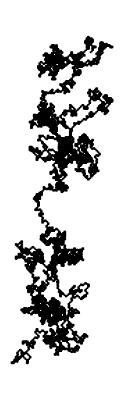

```mathematica
Graphics[Line[AnglePath[90° Mod[Prime[Range[10000]],4]]]]
```

```mathematica
16^^ffa5
```

65445

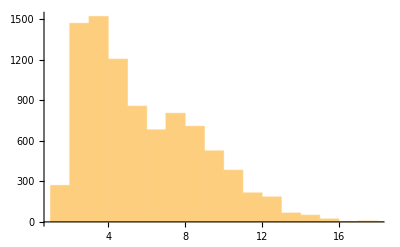

```mathematica
Histogram@StringLength[TextWords[WikipediaData["computers"]]]
```